# Лабораторная работа №2

## Математические модели колебательных движений механических систем: пружинный осцилятор и математический маятник

## Объект моделирования -- пружинный осциллятор

### Концептуальная постановка задачи

Объектом исследования является физическое тело массы m, которое находится на одном 
конце пружины, второй конец пружины жестко закреплен. Тело имеет небольшие размеры по 
сравнению с длиной пружины, поэтому принимаем его за материальную точку.

Тело движется вперед или назад по горизонтальной поверхности без трения. Допущение об 
отсутствии трения справедливо для небольших промежутков времени. Обозначим через r(t) 
координату тела вдоль оси пружины относительно положения равновесия r = 0, когда пружина 
не сжата и не растянута. Будем считать, что r(t) > 0, когда пружина растянута и r(t) < 0, когда она сжата.

Тело находится под действием силы упругости пружины; жесткость пружины k = const > 0. Сила упругости описывается законом Гука F = -k r. Закон Гука справедлив при небольших 
отклонениях пружины от ее положения равновесия.

Расстояние между точкой нейтрального положения пружины r = 0 и стенкой, к которой крепится пружина, равно  L.

Принимая во внимание, что в некоторый момент времени пружину растянули на величину r0 и 
сообщили телу скорость v0, требуется определить координату тела r(t) как функцию времени.

## Задание 1. Область применимости модели пружинного осциллятора

```mathematica
r[t]/.DSolve[{r''[t]==-ω^2 r[t],r[0]==r0,r'[0]==v0},r[t],t]
```

{(r0 ω Cos[t ω]+v0 Sin[t ω])/ω}

```mathematica
Solve[{%==L},v0]
Solve[{%%==L},r0]
```

{{v0→ω (L-r0 Cos[t ω]) Csc[t ω]}}

{{r0→(Sec[t ω] (L ω-v0 Sin[t ω]))/ω}}

```mathematica
DSolve[{m r''[t]==-k r[t],r[0]==r0,r'[0]==v0},r[t],t]//Simplify
```

{{r[t]→r0 Cos[(√k t)/(√m)]+(√m v0 Sin[(√k t)/(√m)])/(√k)}}

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
```

```mathematica
Manipulate[Plot[{
Evaluate[r[t]/.NDSolve[{m r''[t]==-k r[t],r[0]==r0,r'[0]==v0},r,{t,0,30},Method->{"EventLocator","Event"->r[t]-l}]],l},{t,0,30}],
{{m,0.3,"m"},0.1,5,Appearance->"Labeled"},
{{k,0.2,"k"},0.1,3,Appearance->"Labeled"},
{{l,2,"l"},1,15,Appearance->"Labeled"},
{{r0,3,"r_0"},0,15,Appearance->"Labeled"},
{{v0,4,"v_0"},0,15,Appearance->"Labeled"}]
```

# Задание 2. Построение модели пружинного осциллятора для подвешенной пружины

### Содержательная постановка задачи

Для системы, в которой тело прикреплено к нижнему концу подвешенной пружины, исследовать колебательные движения тела с учетом силы тяжести и сопротивления среды. Масса тела m, жесткость пружины k, коэффициент сопротивления среды μ и растяжение пружины за счет приложенной массы L известны.

### Задание

По содержательной постановке задачи сформулируйте концептуальную поставку задачи и 
постройте математическую модель (например, на основании второго закона Ньютона).
При построении модели учитывайте тот факт, что в состоянии равновесия суммарная сила, 
действующая на тело, равна gm - kL == 0.

### Концептуальная постановка задачи

Объектом исследования является физическое тело массы m, которое находится на одном 
конце пружины, второй конец пружины жестко закреплен. Тело имеет небольшие размеры по 
сравнению с длиной пружины, поэтому принимаем его за материальную точку.

Тело движется вверх или низ по вертикальной поверхности с учётом сопротивления среды. Обозначим через r(t) координату тела вдоль оси пружины относительно положения равновесия r = 0, когда сила тяжести будет скомпенсирована некоторым начальным растяжением пружины.

Тело находится под действием силы упругости пружины; жесткость пружины k = const > 0. Сила упругости описывается законом Гука F = -k r. Закон Гука справедлив при небольших 
отклонениях пружины от ее положения равновесия.

Тело находится под действием силы сопротивления среды, коэффициент сопротивления среды μ=const . Сила трения описывается следующим образом: F=-μr’ (справедливо при движении тела: r’ != 0)

Расстояние между точкой нейтрального положения пружины r = 0 и положением, когда 
пружина сжата за счёт отсутствия приложенных сил, равно  -L.

Принимая во внимание, что в некоторый момент времени пружину растянули на величину r0 и 
сообщили телу скорость v0, требуется определить координату тела r(t) как функцию времени.

## Задание 3. Модель пружинного осциллятора с учетом трения

Рассмотрим математическую модель пружинного осциллятора с учетом сопротивления среды

```mathematica
k31=1;
k32=1-10^(-2n);
k33=1+10^(-2n);
```

```mathematica
DSolve[{r''[t]==-k31 r[t]-2 r'[t],r[0]==0,r'[0]==1},r[t],t]
```

{{r[t]→ⅇ^-t t}}

```mathematica
DSolve[{r''[t]==-k32 r[t]-2 r'[t],r[0]==0,r'[0]==1},r[t],t]
```

{{r[t]→-2^(-1+n) 5^n (ⅇ^((-1-10^-n) t)-ⅇ^((-1+10^-n) t))}}

```mathematica
DSolve[{r''[t]==-k33 r[t]-2 r'[t],r[0]==0,r'[0]==1},r[t],t]
```

{{r[t]→10^n ⅇ^-t Sin[10^-n t]}}

```mathematica
r31[n_,t_]:=ⅇ^-t t;
r32[n_,t_]:=10^n ⅇ^-t Sinh[10^-n t];
r33[n_,t_]:=10^n ⅇ^-t Sin[10^-n t];
```

```mathematica
Manipulate[Plot[{r31[n,t],r32[n,t],r33[n,t]},{t,-10,10},PlotLegends->{"r1","r2","r3"}],{{n,0.3,"n"},0,4,Appearance->"Labeled"}]
```

```mathematica
r31[n,t]
Limit[r32[n,t],n->∞]
Limit[r33[n,t],n->∞]
```

ⅇ^-t t

ⅇ^-t t

ⅇ^-t t

## Задание 4. Модель пружинного осциллятора под действием внешней силы

Тело, закрепленное на пружине, совершает незатухающие колебания.Предположим, что на тело действует внешняя сила F (t) = F0 cos3 (t ω2).Покажите, что существует два значения внешней частоты ω2, при которых возникает резонанс (усиление собственных колебаний системы с частотой ω = k/m под действием внешней силы), и найдите их оба.

```mathematica
r41=(DSolve[{r''[t]+ω0^2 r[t]==F0 Cos[t ω2]^3},r[t],t]//Simplify)[[1,1,2]]
```

1/(4 (ω0^4-10 ω0^2 ω2^2+9 ω2^4))(4 (ω0^4-10 ω0^2 ω2^2+9 ω2^4) C[1] Cos[t ω0]+3 F0 (ω0^2-9 ω2^2) Cos[t ω2]+(ω0^2-ω2^2) (F0 Cos[3 t ω2]+4 (ω0^2-9 ω2^2) C[2] Sin[t ω0]))

```mathematica
Solve[ω0^4-10 ω0^2 ω2^2+9 ω2^4==0,ω2]
```

{{ω2→-ω0},{ω2→-ω0/3},{ω2→ω0/3},{ω2→ω0}}

Следовательно, явление резонанса будет при ω2^2→ω0^2 и ω2^2→ω0^2/3

## Задание 5. Модель маятника без учета трения

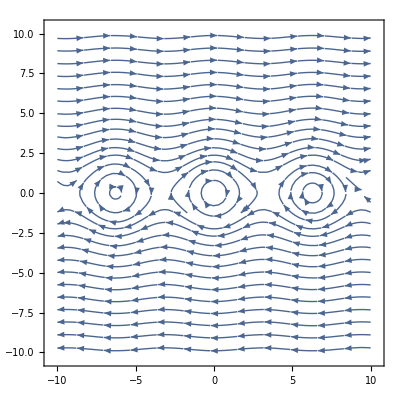

```mathematica
StreamPlot[{ω, -Sin[α]},{α, -10,10}, {ω, -10,10}]
```

```mathematica
(*Manipulate[ContourPlot[ω^2==2Cos[α]+2Cc, {α,-10,10}, {ω,-10,10}], {{Cc, 1,1},-1,10,1, Appearance->"Labeled"}]*)
```